```mathematica
cross[{a_,b_},{c_,d_}]=-b c + a d
```

-b c+a d

```mathematica
f[x,y]
```

f[x,y]

```mathematica
H[x_,y_]=D[D[f[x Cos[θ]+y Sin[θ],-x Sin[θ]+y Cos[θ]],{{x,y}}],{{x,y}}]
```

{{-Sin[θ] (-Sin[θ] f^(0,2)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]+Cos[θ] f^(1,1)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]])+Cos[θ] (-Sin[θ] f^(1,1)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]+Cos[θ] f^(2,0)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]),-Sin[θ] (Cos[θ] f^(0,2)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]+Sin[θ] f^(1,1)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]])+Cos[θ] (Cos[θ] f^(1,1)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]+Sin[θ] f^(2,0)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]])},{Cos[θ] (-Sin[θ] f^(0,2)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]+Cos[θ] f^(1,1)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]])+Sin[θ] (-Sin[θ] f^(1,1)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]+Cos[θ] f^(2,0)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]),Cos[θ] (Cos[θ] f^(0,2)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]+Sin[θ] f^(1,1)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]])+Sin[θ] (Cos[θ] f^(1,1)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]+Sin[θ] f^(2,0)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]])}}

```mathematica
FullSimplify[Tr[H[x,y]]]
FullSimplify[Det[H[x,y]]]
```

f^(0,2)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]+f^(2,0)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]

-(f^(1,1)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]])^2+f^(0,2)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]] f^(2,0)[x Cos[θ]+y Sin[θ],y Cos[θ]-x Sin[θ]]

```mathematica
({{λ1[x_,y_], λ2[x_,y_]}, {v1[x_,y_], v2[x_,y_]}})=Eigensystem[H[x,y]];
```

```mathematica
FullSimplify[FullSimplify[v1[x,y]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[2,0][f][c x+s y,-s x+c y]->t11,Derivative[1,1][f][c x+s y,-s x+c y]->t12,Derivative[0,2][f][c x+s y,-s x+c y]->t22}]/.{c->Cos[θ],s->Sin[θ]}]
```

{(-√(4 t12^2+(t11-t22)^2)+(t11-t22) Cos[2 θ]-2 t12 Sin[2 θ])/(2 t12 Cos[2 θ]+(t11-t22) Sin[2 θ]),1}

## First order derivatives

```mathematica
f1=FullSimplify[D[f[x Cos[θ]+y Sin[θ],-x Sin[θ]+y Cos[θ]],x]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[1,0][f][c x+s y,-s x+c y]->t1,Derivative[0,1][f][c x+s y,-s x+c y]->t2}]
f2=FullSimplify[D[f[x Cos[θ]+y Sin[θ],-x Sin[θ]+y Cos[θ]],y]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[1,0][f][c x+s y,-s x+c y]->t1,Derivative[0,1][f][c x+s y,-s x+c y]->t2}]
```

c t1-s t2

s t1+c t2

```mathematica
FullSimplify[f1^2+f2^2/.s->√(1-c^2)]
```

t1^2+t2^2

```mathematica
FullSimplify[a f1^2+ f2^2/.s->√(1-c^2)/.Solve[D[a f1^2+ f2^2/.s->√(1-c^2),c]==0,a]]
```

{t1^2+t2^2}

## Second order derivatives

```mathematica
f11=FullSimplify[D[f[x Cos[θ]+y Sin[θ],-x Sin[θ]+y Cos[θ]],x,x]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[2,0][f][c x+s y,-s x+c y]->t11,Derivative[1,1][f][c x+s y,-s x+c y]->t12,Derivative[0,2][f][c x+s y,-s x+c y]->t22}]
f12=FullSimplify[D[f[x Cos[θ]+y Sin[θ],-x Sin[θ]+y Cos[θ]],x,y]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[2,0][f][c x+s y,-s x+c y]->t11,Derivative[1,1][f][c x+s y,-s x+c y]->t12,Derivative[0,2][f][c x+s y,-s x+c y]->t22}]
f22=FullSimplify[D[f[x Cos[θ]+y Sin[θ],-x Sin[θ]+y Cos[θ]],y,y]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[2,0][f][c x+s y,-s x+c y]->t11,Derivative[1,1][f][c x+s y,-s x+c y]->t12,Derivative[0,2][f][c x+s y,-s x+c y]->t22}]
```

c^2 t11-2 c s t12+s^2 t22

c (s t11+c t12)-s (s t12+c t22)

s^2 t11+2 c s t12+c^2 t22

```mathematica
FullSimplify[f11+f22/.s->√(1-c^2)]
FullSimplify[f11 f22-f12^2/.s->√(1-c^2)]
```

t11+t22

-t12^2+t11 t22

```mathematica
f12
```

c (s t11+c t12)-s (s t12+c t22)

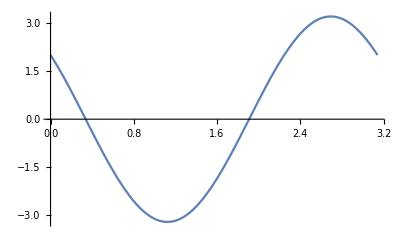

```mathematica
Block[{t11=1,t12=2,t22=6},
Plot[(f12/.{c->Cos[θ],s->Sin[θ]}),{θ,0,π}]
]
```

## Third order derivatives

```mathematica
f111=FullSimplify[D[f[x Cos[θ]+y Sin[θ],-x Sin[θ]+y Cos[θ]],x,x,x]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[3,0][f][c x+s y,-s x+c y]->t111,Derivative[2,1][f][c x+s y,-s x+c y]->t112,Derivative[1,2][f][c x+s y,-s x+c y]->t122,Derivative[0,3][f][c x+s y,-s x+c y]->t222}]
f112=FullSimplify[D[f[x Cos[θ]+y Sin[θ],-x Sin[θ]+y Cos[θ]],x,x,y]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[3,0][f][c x+s y,-s x+c y]->t111,Derivative[2,1][f][c x+s y,-s x+c y]->t112,Derivative[1,2][f][c x+s y,-s x+c y]->t122,Derivative[0,3][f][c x+s y,-s x+c y]->t222}]
f122=FullSimplify[D[f[x Cos[θ]+y Sin[θ],-x Sin[θ]+y Cos[θ]],x,y,y]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[3,0][f][c x+s y,-s x+c y]->t111,Derivative[2,1][f][c x+s y,-s x+c y]->t112,Derivative[1,2][f][c x+s y,-s x+c y]->t122,Derivative[0,3][f][c x+s y,-s x+c y]->t222}]
f222=FullSimplify[D[f[x Cos[θ]+y Sin[θ],-x Sin[θ]+y Cos[θ]],y,y,y]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[3,0][f][c x+s y,-s x+c y]->t111,Derivative[2,1][f][c x+s y,-s x+c y]->t112,Derivative[1,2][f][c x+s y,-s x+c y]->t122,Derivative[0,3][f][c x+s y,-s x+c y]->t222}]
```

c^3 t111-3 c^2 s t112+3 c s^2 t122-s^3 t222

c^3 t112+c^2 s (t111-2 t122)+s^3 t122+c s^2 (-2 t112+t222)

-s^3 t112+c s^2 (t111-2 t122)+c^3 t122+c^2 s (2 t112-t222)

s^3 t111+3 c s^2 t112+3 c^2 s t122+c^3 t222

```mathematica
FullSimplify[10(f112^2+f122^2)-4(f111 f122+f112 f222)+2(f111^2+f222^2)/.s->√(1-c^2)]
```

2 (t111^2-2 t111 t122+5 (t112^2+t122^2)-2 t112 t222+t222^2)

### Invariants

```mathematica
i1=FullSimplify[D[Tr[H[x,y]],{{x,y}}].D[Tr[H[x,y]],{{x,y}}]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[3,0][f][c x+s y,-s x+c y]->t111,Derivative[2,1][f][c x+s y,-s x+c y]->t112,Derivative[1,2][f][c x+s y,-s x+c y]->t122,Derivative[0,3][f][c x+s y,-s x+c y]->t222}/.s->√(1-c^2)]
```

(t111+t122)^2+(t112+t222)^2

```mathematica
i2=FullSimplify[D[Det[H[x,y]],{{x,y}}].D[Det[H[x,y]],{{x,y}}]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[2,0][f][c x+s y,-s x+c y]->t11,Derivative[1,1][f][c x+s y,-s x+c y]->t12,Derivative[0,2][f][c x+s y,-s x+c y]->t22,Derivative[3,0][f][c x+s y,-s x+c y]->t111,Derivative[2,1][f][c x+s y,-s x+c y]->t112,Derivative[1,2][f][c x+s y,-s x+c y]->t122,Derivative[0,3][f][c x+s y,-s x+c y]->t222}/.s->√(1-c^2)]
```

4 t12^2 t122^2+t111^2 t22^2-4 t112 t12 (t11 t122+(t111+t122) t22)+t112^2 (4 t12^2+t22^2)+2 t11 t112 t22 t222+2 t11 t122 (t111 t22-2 t12 t222)+t11^2 (t122^2+t222^2)

```mathematica
i3=FullSimplify[cross[D[Tr[H[x,y]],{{x,y}}],D[Det[H[x,y]],{{x,y}}]]/.{Sin[θ]->s,Cos[θ]->c}/.{Derivative[2,0][f][c x+s y,-s x+c y]->t11,Derivative[1,1][f][c x+s y,-s x+c y]->t12,Derivative[0,2][f][c x+s y,-s x+c y]->t22,Derivative[3,0][f][c x+s y,-s x+c y]->t111,Derivative[2,1][f][c x+s y,-s x+c y]->t112,Derivative[1,2][f][c x+s y,-s x+c y]->t122,Derivative[0,3][f][c x+s y,-s x+c y]->t222}/.s->√(1-c^2)]
```

2 t112^2 t12-2 t12 t122 (t111+t122)+t111 (t11-t22) t222+t112 (-t11 t122+t122 t22+2 t12 t222)

```mathematica
i1
i2
i3
```

(t111+t122)^2+(t112+t222)^2

4 t12^2 t122^2+t111^2 t22^2-4 t112 t12 (t11 t122+(t111+t122) t22)+t112^2 (4 t12^2+t22^2)+2 t11 t112 t22 t222+2 t11 t122 (t111 t22-2 t12 t222)+t11^2 (t122^2+t222^2)

2 t112^2 t12-2 t12 t122 (t111+t122)+t111 (t11-t22) t222+t112 (-t11 t122+t122 t22+2 t12 t222)